```mathematica
Quit
```

```mathematica
MD=Simplify[{{0,0,1/hy^4,0,0},{0, 2/hx^2/hy^2,-4(1/hy^4+1/hx^2/hy^2),2/hx^2/hy^2,0},{1/hx^4,-4(1/hx^4+1/hx^2/hy^2), 6(1/hx^4+1/hy^4)+8/hx^2/hy^2,-4(1/hx^4+1/hx^2/hy^2),1/hx^4},{0, 2/hx^2/hy^2,-4(1/hy^4+1/hx^2/hy^2),2/hx^2/hy^2,0},{0,0,1/hy^4,0,0}}];
MB1X=Simplify[{{0, -ν/hy^2, 0},{1/hx^2,2(ν/hy^2-1/hx^2), 1/hx^2},{0,-ν/hy^2,0}}];
MB1Y=Simplify[-{{0, -1/hy^2, 0},{ν/hx^2,2(1/hy^2-ν/hx^2), ν/hx^2},{0,-1/hy^2,0}}];
MB2X=Simplify[{{0,0,0,0,0},{0, -(2+ν)/hy^2, 0, (2+ν)/hy^2,0},{-1/hx^2,2((2+ν)/hy^2+1/hx^2),0,-2((2+ν)/hy^2+1/hx^2), 1/hx^2},{0, -(2+ν)/hy^2, 0, (2+ν)/hy^2,0},{0,0,0,0,0}}];
MB2Y=Simplify[-{{0,0,1/hy^2,0,0},{0, (2+ν)/hx^2, -2((2+ν)/hx^2+1/hy^2), (2+ν)/hx^2,0},{0,0,0,0,0},{0, -(2+ν)/hx^2, 2((2+ν)/hx^2+1/hy^2), -(2+ν)/hx^2,0},{0,0,-1/hy^2,0,0}}];
MC=Simplify[{{1/hx^2/hy^2, 0, -1/hx^2/hy^2},{0,0,0},{-1/hx^2/hy^2,0,1/hx^2/hy^2}}];
```

```mathematica
MatrixForm[MD]
```

(0 | 0 | 1/hy^4 | 0 | 0
0 | 2/(hx^2 hy^2) | -4 (1/hy^4+1/(hx^2 hy^2)) | 2/(hx^2 hy^2) | 0
1/hx^4 | -4 (1/hx^4+1/(hx^2 hy^2)) | 6 (1/hx^4+1/hy^4)+8/(hx^2 hy^2) | -4 (1/hx^4+1/(hx^2 hy^2)) | 1/hx^4
0 | 2/(hx^2 hy^2) | -4 (1/hy^4+1/(hx^2 hy^2)) | 2/(hx^2 hy^2) | 0
0 | 0 | 1/hy^4 | 0 | 0)

```mathematica
MatrixForm[MB1X]
```

(0 | -ν/hy^2 | 0
1/hx^2 | -2/hx^2+(2 ν)/hy^2 | 1/hx^2
0 | -ν/hy^2 | 0)

```mathematica
MatrixForm[MB1Y]
```

(0 | 1/hy^2 | 0
-ν/hx^2 | -2/hy^2+(2 ν)/hx^2 | -ν/hx^2
0 | 1/hy^2 | 0)

```mathematica
MatrixForm[MB2X]
```

(0 | 0 | 0 | 0 | 0
0 | -(2+ν)/hy^2 | 0 | (2+ν)/hy^2 | 0
-1/hx^2 | 2 (1/hx^2+(2+ν)/hy^2) | 0 | -2 (1/hx^2+(2+ν)/hy^2) | 1/hx^2
0 | -(2+ν)/hy^2 | 0 | (2+ν)/hy^2 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[MB2Y]
```

(0 | 0 | -1/hy^2 | 0 | 0
0 | -(2+ν)/hx^2 | 2 (1/hy^2+(2+ν)/hx^2) | -(2+ν)/hx^2 | 0
0 | 0 | 0 | 0 | 0
0 | (2+ν)/hx^2 | -2 (1/hy^2+(2+ν)/hx^2) | (2+ν)/hx^2 | 0
0 | 0 | 1/hy^2 | 0 | 0)

```mathematica
MatrixForm[MC]
```

(1/(hx^2 hy^2) | 0 | -1/(hx^2 hy^2)
0 | 0 | 0
-1/(hx^2 hy^2) | 0 | 1/(hx^2 hy^2))

```mathematica
Clear[i,j]
```

```mathematica
EQ[i_,j_]=Sum[MD[[3-q,3-p]]F[i-p,j-q],{p,2,-2, -1},{q,2,-2, -1}]
```

F[-2+i,j]/hx^4+(2 F[-1+i,-1+j])/(hx^2 hy^2)-4 (1/hx^4+1/(hx^2 hy^2)) F[-1+i,j]+(2 F[-1+i,1+j])/(hx^2 hy^2)+F[i,-2+j]/hy^4-4 (1/hy^4+1/(hx^2 hy^2)) F[i,-1+j]+(6 (1/hx^4+1/hy^4)+8/(hx^2 hy^2)) F[i,j]-4 (1/hy^4+1/(hx^2 hy^2)) F[i,1+j]+F[i,2+j]/hy^4+(2 F[1+i,-1+j])/(hx^2 hy^2)-4 (1/hx^4+1/(hx^2 hy^2)) F[1+i,j]+(2 F[1+i,1+j])/(hx^2 hy^2)+F[2+i,j]/hx^4

```mathematica
BQ1L[j_]=Sum[MB1X[[2-q,2-p]]F[0-p,j-q],{p,1,-1,-1},{q,1,-1,-1}]
```

F[-1,j]/hx^2-(ν F[0,-1+j])/hy^2+(-2/hx^2+(2 ν)/hy^2) F[0,j]-(ν F[0,1+j])/hy^2+F[1,j]/hx^2

```mathematica
BQ1R[j_]=Sum[MB1X[[2-q,2-p]]F[Nx-p,j-q],{p,1,-1,-1},{q,1,-1,-1}]
```

F[-1+Nx,j]/hx^2-(ν F[Nx,-1+j])/hy^2+(-2/hx^2+(2 ν)/hy^2) F[Nx,j]-(ν F[Nx,1+j])/hy^2+F[1+Nx,j]/hx^2

```mathematica
BQ1T[i_]=Sum[MB1Y[[2-q,2-p]]F[i-p,0-q],{p,1,-1,-1},{q,1,-1,-1}]
```

-(ν F[-1+i,0])/hx^2+F[i,-1]/hy^2+(-2/hy^2+(2 ν)/hx^2) F[i,0]+F[i,1]/hy^2-(ν F[1+i,0])/hx^2

```mathematica
BQ1B[i_]=Sum[MB1Y[[2-q,2-p]]F[i-p,Ny-q],{p,1,-1,-1},{q,1,-1,-1}]
```

-(ν F[-1+i,Ny])/hx^2+F[i,-1+Ny]/hy^2+(-2/hy^2+(2 ν)/hx^2) F[i,Ny]+F[i,1+Ny]/hy^2-(ν F[1+i,Ny])/hx^2

```mathematica
BQ2L[j_]=Sum[MB2X[[3-q,3-p]]F[0-p,j-q],{p,2,-2,-1},{q,2,-2,-1}]
```

-F[-2,j]/hx^2-((2+ν) F[-1,-1+j])/hy^2+2 (1/hx^2+(2+ν)/hy^2) F[-1,j]-((2+ν) F[-1,1+j])/hy^2+((2+ν) F[1,-1+j])/hy^2-2 (1/hx^2+(2+ν)/hy^2) F[1,j]+((2+ν) F[1,1+j])/hy^2+F[2,j]/hx^2

```mathematica
BQ2R[j_]=Sum[MB2X[[3-q,3-p]]F[Nx-p,j-q],{p,2,-2,-1},{q,2,-2,-1}]
```

-F[-2+Nx,j]/hx^2-((2+ν) F[-1+Nx,-1+j])/hy^2+2 (1/hx^2+(2+ν)/hy^2) F[-1+Nx,j]-((2+ν) F[-1+Nx,1+j])/hy^2+((2+ν) F[1+Nx,-1+j])/hy^2-2 (1/hx^2+(2+ν)/hy^2) F[1+Nx,j]+((2+ν) F[1+Nx,1+j])/hy^2+F[2+Nx,j]/hx^2

```mathematica
BQ2T[i_]=Sum[MB2Y[[3-q,3-p]]F[i-p,0-q],{p,2,-2,-1},{q,2,-2,-1}]
```

-((2+ν) F[-1+i,-1])/hx^2+((2+ν) F[-1+i,1])/hx^2-F[i,-2]/hy^2+2 (1/hy^2+(2+ν)/hx^2) F[i,-1]-2 (1/hy^2+(2+ν)/hx^2) F[i,1]+F[i,2]/hy^2-((2+ν) F[1+i,-1])/hx^2+((2+ν) F[1+i,1])/hx^2

```mathematica
BQ2B[i_]=Sum[MB2Y[[3-q,3-p]]F[i-p,Ny-q],{p,2,-2,-1},{q,2,-2,-1}]
```

-((2+ν) F[-1+i,-1+Ny])/hx^2+((2+ν) F[-1+i,1+Ny])/hx^2-F[i,-2+Ny]/hy^2+2 (1/hy^2+(2+ν)/hx^2) F[i,-1+Ny]-2 (1/hy^2+(2+ν)/hx^2) F[i,1+Ny]+F[i,2+Ny]/hy^2-((2+ν) F[1+i,-1+Ny])/hx^2+((2+ν) F[1+i,1+Ny])/hx^2

```mathematica
CQLT=Sum[MC[[2-q,2-p]]F[0-p,0-q],{p,1,-1,-1},{q,1,-1,-1}]
CQLB=Sum[MC[[2-q,2-p]]F[0-p,Ny-q],{p,1,-1,-1},{q,1,-1,-1}]
CQRT=Sum[MC[[2-q,2-p]]F[Nx-p,0-q],{p,1,-1,-1},{q,1,-1,-1}]
CQRB=Sum[MC[[2-q,2-p]]F[Nx-p,Ny-q],{p,1,-1,-1},{q,1,-1,-1}]
```

F[-1,-1]/(hx^2 hy^2)-F[-1,1]/(hx^2 hy^2)-F[1,-1]/(hx^2 hy^2)+F[1,1]/(hx^2 hy^2)

F[-1,-1+Ny]/(hx^2 hy^2)-F[-1,1+Ny]/(hx^2 hy^2)-F[1,-1+Ny]/(hx^2 hy^2)+F[1,1+Ny]/(hx^2 hy^2)

F[-1+Nx,-1]/(hx^2 hy^2)-F[-1+Nx,1]/(hx^2 hy^2)-F[1+Nx,-1]/(hx^2 hy^2)+F[1+Nx,1]/(hx^2 hy^2)

F[-1+Nx,-1+Ny]/(hx^2 hy^2)-F[-1+Nx,1+Ny]/(hx^2 hy^2)-F[1+Nx,-1+Ny]/(hx^2 hy^2)+F[1+Nx,1+Ny]/(hx^2 hy^2)

```mathematica
(* j=0 *)
```

```mathematica
E00=Expand[EQ[0, 0]+BQ2L[0]/hx^2+BQ2T[0]/hy^2+2(BQ1L[0]/hx^2+BQ1T[0]/hy^2)+2(1+ν)CQLT +2ν BQ1L[1]/hy^2+2ν BQ1T[1]/hx^2]
```

(2 F[0,0])/hx^4+(2 F[0,0])/hy^4+(8 F[0,0])/(hx^2 hy^2)+(8 ν F[0,0])/(hx^2 hy^2)-(2 ν^2 F[0,0])/hx^4-(2 ν^2 F[0,0])/hy^4-(4 F[0,1])/hy^4-(8 F[0,1])/(hx^2 hy^2)-(8 ν F[0,1])/(hx^2 hy^2)+(4 ν^2 F[0,1])/hy^4+(2 F[0,2])/hy^4-(2 ν^2 F[0,2])/hy^4-(4 F[1,0])/hx^4-(8 F[1,0])/(hx^2 hy^2)-(8 ν F[1,0])/(hx^2 hy^2)+(4 ν^2 F[1,0])/hx^4+(8 F[1,1])/(hx^2 hy^2)+(8 ν F[1,1])/(hx^2 hy^2)+(2 F[2,0])/hx^4-(2 ν^2 F[2,0])/hx^4

```mathematica
E10=Expand[EQ[1, 0]+BQ2T[1]/hy^2-BQ1L[0]/hx^2+2BQ1T[1]/hy^2-2ν BQ1T[1]/hx^2+ν BQ1T[2]/hx^2]
```

-(2 F[0,0])/hx^4-(4 F[0,0])/(hx^2 hy^2)-(4 ν F[0,0])/(hx^2 hy^2)+(2 ν^2 F[0,0])/hx^4+(4 F[0,1])/(hx^2 hy^2)+(2 ν F[0,1])/(hx^2 hy^2)+(5 F[1,0])/hx^4+(2 F[1,0])/hy^4+(8 F[1,0])/(hx^2 hy^2)+(8 ν F[1,0])/(hx^2 hy^2)-(5 ν^2 F[1,0])/hx^4-(4 F[1,1])/hy^4-(8 F[1,1])/(hx^2 hy^2)-(4 ν F[1,1])/(hx^2 hy^2)+(2 F[1,2])/hy^4-(4 F[2,0])/hx^4-(4 F[2,0])/(hx^2 hy^2)-(4 ν F[2,0])/(hx^2 hy^2)+(4 ν^2 F[2,0])/hx^4+(4 F[2,1])/(hx^2 hy^2)+(2 ν F[2,1])/(hx^2 hy^2)+F[3,0]/hx^4-(ν^2 F[3,0])/hx^4

```mathematica
Ei0=Expand[EQ[i, 0]+BQ2T[i]/hy^2+2BQ1T[i]/hy^2-2ν BQ1T[i]/hx^2+ν (BQ1T[i-1]/hx^2+BQ1T[i+1]/hx^2)]
```

F[-2+i,0]/hx^4-(ν^2 F[-2+i,0])/hx^4-(4 F[-1+i,0])/hx^4-(4 F[-1+i,0])/(hx^2 hy^2)-(4 ν F[-1+i,0])/(hx^2 hy^2)+(4 ν^2 F[-1+i,0])/hx^4+(4 F[-1+i,1])/(hx^2 hy^2)+(2 ν F[-1+i,1])/(hx^2 hy^2)+(6 F[i,0])/hx^4+(2 F[i,0])/hy^4+(8 F[i,0])/(hx^2 hy^2)+(8 ν F[i,0])/(hx^2 hy^2)-(6 ν^2 F[i,0])/hx^4-(4 F[i,1])/hy^4-(8 F[i,1])/(hx^2 hy^2)-(4 ν F[i,1])/(hx^2 hy^2)+(2 F[i,2])/hy^4-(4 F[1+i,0])/hx^4-(4 F[1+i,0])/(hx^2 hy^2)-(4 ν F[1+i,0])/(hx^2 hy^2)+(4 ν^2 F[1+i,0])/hx^4+(4 F[1+i,1])/(hx^2 hy^2)+(2 ν F[1+i,1])/(hx^2 hy^2)+F[2+i,0]/hx^4-(ν^2 F[2+i,0])/hx^4

```mathematica
ENxm10=Expand[EQ[Nx-1, 0]+BQ2T[Nx-1]/hy^2-BQ1R[0]/hx^2+2BQ1T[Nx-1]/hy^2-2ν BQ1T[Nx-1]/hx^2+ν BQ1T[Nx-2]/hx^2]
```

F[-3+Nx,0]/hx^4-(ν^2 F[-3+Nx,0])/hx^4-(4 F[-2+Nx,0])/hx^4-(4 F[-2+Nx,0])/(hx^2 hy^2)-(4 ν F[-2+Nx,0])/(hx^2 hy^2)+(4 ν^2 F[-2+Nx,0])/hx^4+(4 F[-2+Nx,1])/(hx^2 hy^2)+(2 ν F[-2+Nx,1])/(hx^2 hy^2)+(5 F[-1+Nx,0])/hx^4+(2 F[-1+Nx,0])/hy^4+(8 F[-1+Nx,0])/(hx^2 hy^2)+(8 ν F[-1+Nx,0])/(hx^2 hy^2)-(5 ν^2 F[-1+Nx,0])/hx^4-(4 F[-1+Nx,1])/hy^4-(8 F[-1+Nx,1])/(hx^2 hy^2)-(4 ν F[-1+Nx,1])/(hx^2 hy^2)+(2 F[-1+Nx,2])/hy^4-(2 F[Nx,0])/hx^4-(4 F[Nx,0])/(hx^2 hy^2)-(4 ν F[Nx,0])/(hx^2 hy^2)+(2 ν^2 F[Nx,0])/hx^4+(4 F[Nx,1])/(hx^2 hy^2)+(2 ν F[Nx,1])/(hx^2 hy^2)

```mathematica
ENx0=Expand[EQ[Nx, 0]-BQ2R[0]/hx^2+BQ2T[Nx]/hy^2+2(BQ1R[0]/hx^2+BQ1T[Nx]/hy^2)-2(1+ν)CQRT+2ν BQ1R[1]/hy^2+2ν BQ1T[Nx-1]/hx^2]
```

(2 F[-2+Nx,0])/hx^4-(2 ν^2 F[-2+Nx,0])/hx^4-(4 F[-1+Nx,0])/hx^4-(8 F[-1+Nx,0])/(hx^2 hy^2)-(8 ν F[-1+Nx,0])/(hx^2 hy^2)+(4 ν^2 F[-1+Nx,0])/hx^4+(8 F[-1+Nx,1])/(hx^2 hy^2)+(8 ν F[-1+Nx,1])/(hx^2 hy^2)+(2 F[Nx,0])/hx^4+(2 F[Nx,0])/hy^4+(8 F[Nx,0])/(hx^2 hy^2)+(8 ν F[Nx,0])/(hx^2 hy^2)-(2 ν^2 F[Nx,0])/hx^4-(2 ν^2 F[Nx,0])/hy^4-(4 F[Nx,1])/hy^4-(8 F[Nx,1])/(hx^2 hy^2)-(8 ν F[Nx,1])/(hx^2 hy^2)+(4 ν^2 F[Nx,1])/hy^4+(2 F[Nx,2])/hy^4-(2 ν^2 F[Nx,2])/hy^4

```mathematica
(* j=1 *)
```

```mathematica
E01=Expand[EQ[0, 1]+BQ2L[1]/hx^2-BQ1T[0]/hy^2+2 BQ1L[1]/hx^2-2ν  BQ1L[1]/hy^2+ν BQ1L[2]/hy^2]
```

-(2 F[0,0])/hy^4-(4 F[0,0])/(hx^2 hy^2)-(4 ν F[0,0])/(hx^2 hy^2)+(2 ν^2 F[0,0])/hy^4+(2 F[0,1])/hx^4+(5 F[0,1])/hy^4+(8 F[0,1])/(hx^2 hy^2)+(8 ν F[0,1])/(hx^2 hy^2)-(5 ν^2 F[0,1])/hy^4-(4 F[0,2])/hy^4-(4 F[0,2])/(hx^2 hy^2)-(4 ν F[0,2])/(hx^2 hy^2)+(4 ν^2 F[0,2])/hy^4+F[0,3]/hy^4-(ν^2 F[0,3])/hy^4+(4 F[1,0])/(hx^2 hy^2)+(2 ν F[1,0])/(hx^2 hy^2)-(4 F[1,1])/hx^4-(8 F[1,1])/(hx^2 hy^2)-(4 ν F[1,1])/(hx^2 hy^2)+(4 F[1,2])/(hx^2 hy^2)+(2 ν F[1,2])/(hx^2 hy^2)+(2 F[2,1])/hx^4

```mathematica
E11=Expand[EQ[1, 1]-BQ1L[1]/hx^2-BQ1T[1]/hy^2]
```

(2 F[0,0])/(hx^2 hy^2)+(2 ν F[0,0])/(hx^2 hy^2)-(2 F[0,1])/hx^4-(4 F[0,1])/(hx^2 hy^2)-(2 ν F[0,1])/(hx^2 hy^2)+(2 F[0,2])/(hx^2 hy^2)+(ν F[0,2])/(hx^2 hy^2)-(2 F[1,0])/hy^4-(4 F[1,0])/(hx^2 hy^2)-(2 ν F[1,0])/(hx^2 hy^2)+(5 F[1,1])/hx^4+(5 F[1,1])/hy^4+(8 F[1,1])/(hx^2 hy^2)-(4 F[1,2])/hy^4-(4 F[1,2])/(hx^2 hy^2)+F[1,3]/hy^4+(2 F[2,0])/(hx^2 hy^2)+(ν F[2,0])/(hx^2 hy^2)-(4 F[2,1])/hx^4-(4 F[2,1])/(hx^2 hy^2)+(2 F[2,2])/(hx^2 hy^2)+F[3,1]/hx^4

```mathematica
Ei1=Expand[EQ[i, 1]-BQ1T[i]/hy^2]
```

F[-2+i,1]/hx^4+(2 F[-1+i,0])/(hx^2 hy^2)+(ν F[-1+i,0])/(hx^2 hy^2)-(4 F[-1+i,1])/hx^4-(4 F[-1+i,1])/(hx^2 hy^2)+(2 F[-1+i,2])/(hx^2 hy^2)-(2 F[i,0])/hy^4-(4 F[i,0])/(hx^2 hy^2)-(2 ν F[i,0])/(hx^2 hy^2)+(6 F[i,1])/hx^4+(5 F[i,1])/hy^4+(8 F[i,1])/(hx^2 hy^2)-(4 F[i,2])/hy^4-(4 F[i,2])/(hx^2 hy^2)+F[i,3]/hy^4+(2 F[1+i,0])/(hx^2 hy^2)+(ν F[1+i,0])/(hx^2 hy^2)-(4 F[1+i,1])/hx^4-(4 F[1+i,1])/(hx^2 hy^2)+(2 F[1+i,2])/(hx^2 hy^2)+F[2+i,1]/hx^4

```mathematica
ENxm11=Expand[EQ[Nx-1, 1]-BQ1R[1]/hx^2-BQ1T[Nx-1]/hy^2]
```

F[-3+Nx,1]/hx^4+(2 F[-2+Nx,0])/(hx^2 hy^2)+(ν F[-2+Nx,0])/(hx^2 hy^2)-(4 F[-2+Nx,1])/hx^4-(4 F[-2+Nx,1])/(hx^2 hy^2)+(2 F[-2+Nx,2])/(hx^2 hy^2)-(2 F[-1+Nx,0])/hy^4-(4 F[-1+Nx,0])/(hx^2 hy^2)-(2 ν F[-1+Nx,0])/(hx^2 hy^2)+(5 F[-1+Nx,1])/hx^4+(5 F[-1+Nx,1])/hy^4+(8 F[-1+Nx,1])/(hx^2 hy^2)-(4 F[-1+Nx,2])/hy^4-(4 F[-1+Nx,2])/(hx^2 hy^2)+F[-1+Nx,3]/hy^4+(2 F[Nx,0])/(hx^2 hy^2)+(2 ν F[Nx,0])/(hx^2 hy^2)-(2 F[Nx,1])/hx^4-(4 F[Nx,1])/(hx^2 hy^2)-(2 ν F[Nx,1])/(hx^2 hy^2)+(2 F[Nx,2])/(hx^2 hy^2)+(ν F[Nx,2])/(hx^2 hy^2)

```mathematica
ENx1=Expand[EQ[Nx, 1]-BQ2R[1]/hx^2-BQ1T[Nx]/hy^2+2 BQ1R[1]/hx^2-2ν  BQ1R[1]/hy^2+ν BQ1R[2]/hy^2]
```

(2 F[-2+Nx,1])/hx^4+(4 F[-1+Nx,0])/(hx^2 hy^2)+(2 ν F[-1+Nx,0])/(hx^2 hy^2)-(4 F[-1+Nx,1])/hx^4-(8 F[-1+Nx,1])/(hx^2 hy^2)-(4 ν F[-1+Nx,1])/(hx^2 hy^2)+(4 F[-1+Nx,2])/(hx^2 hy^2)+(2 ν F[-1+Nx,2])/(hx^2 hy^2)-(2 F[Nx,0])/hy^4-(4 F[Nx,0])/(hx^2 hy^2)-(4 ν F[Nx,0])/(hx^2 hy^2)+(2 ν^2 F[Nx,0])/hy^4+(2 F[Nx,1])/hx^4+(5 F[Nx,1])/hy^4+(8 F[Nx,1])/(hx^2 hy^2)+(8 ν F[Nx,1])/(hx^2 hy^2)-(5 ν^2 F[Nx,1])/hy^4-(4 F[Nx,2])/hy^4-(4 F[Nx,2])/(hx^2 hy^2)-(4 ν F[Nx,2])/(hx^2 hy^2)+(4 ν^2 F[Nx,2])/hy^4+F[Nx,3]/hy^4-(ν^2 F[Nx,3])/hy^4

```mathematica
(* j=j *)
```

```mathematica
E0j=Expand[EQ[0, j]+BQ2L[j]/hx^2+2BQ1L[j]/hx^2-2ν BQ1L[j]/hy^2+ν(BQ1L[j-1]+BQ1L[j+1])/hy^2]
```

F[0,-2+j]/hy^4-(ν^2 F[0,-2+j])/hy^4-(4 F[0,-1+j])/hy^4-(4 F[0,-1+j])/(hx^2 hy^2)-(4 ν F[0,-1+j])/(hx^2 hy^2)+(4 ν^2 F[0,-1+j])/hy^4+(2 F[0,j])/hx^4+(6 F[0,j])/hy^4+(8 F[0,j])/(hx^2 hy^2)+(8 ν F[0,j])/(hx^2 hy^2)-(6 ν^2 F[0,j])/hy^4-(4 F[0,1+j])/hy^4-(4 F[0,1+j])/(hx^2 hy^2)-(4 ν F[0,1+j])/(hx^2 hy^2)+(4 ν^2 F[0,1+j])/hy^4+F[0,2+j]/hy^4-(ν^2 F[0,2+j])/hy^4+(4 F[1,-1+j])/(hx^2 hy^2)+(2 ν F[1,-1+j])/(hx^2 hy^2)-(4 F[1,j])/hx^4-(8 F[1,j])/(hx^2 hy^2)-(4 ν F[1,j])/(hx^2 hy^2)+(4 F[1,1+j])/(hx^2 hy^2)+(2 ν F[1,1+j])/(hx^2 hy^2)+(2 F[2,j])/hx^4

```mathematica
E1j=Expand[EQ[1, j]-BQ1L[j]/hx^2]
```

(2 F[0,-1+j])/(hx^2 hy^2)+(ν F[0,-1+j])/(hx^2 hy^2)-(2 F[0,j])/hx^4-(4 F[0,j])/(hx^2 hy^2)-(2 ν F[0,j])/(hx^2 hy^2)+(2 F[0,1+j])/(hx^2 hy^2)+(ν F[0,1+j])/(hx^2 hy^2)+F[1,-2+j]/hy^4-(4 F[1,-1+j])/hy^4-(4 F[1,-1+j])/(hx^2 hy^2)+(5 F[1,j])/hx^4+(6 F[1,j])/hy^4+(8 F[1,j])/(hx^2 hy^2)-(4 F[1,1+j])/hy^4-(4 F[1,1+j])/(hx^2 hy^2)+F[1,2+j]/hy^4+(2 F[2,-1+j])/(hx^2 hy^2)-(4 F[2,j])/hx^4-(4 F[2,j])/(hx^2 hy^2)+(2 F[2,1+j])/(hx^2 hy^2)+F[3,j]/hx^4

```mathematica
Eij=EQ[i,j]
```

F[-2+i,j]/hx^4+(2 F[-1+i,-1+j])/(hx^2 hy^2)-4 (1/hx^4+1/(hx^2 hy^2)) F[-1+i,j]+(2 F[-1+i,1+j])/(hx^2 hy^2)+F[i,-2+j]/hy^4-4 (1/hy^4+1/(hx^2 hy^2)) F[i,-1+j]+(6 (1/hx^4+1/hy^4)+8/(hx^2 hy^2)) F[i,j]-4 (1/hy^4+1/(hx^2 hy^2)) F[i,1+j]+F[i,2+j]/hy^4+(2 F[1+i,-1+j])/(hx^2 hy^2)-4 (1/hx^4+1/(hx^2 hy^2)) F[1+i,j]+(2 F[1+i,1+j])/(hx^2 hy^2)+F[2+i,j]/hx^4

```mathematica
ENxm1j=Expand[EQ[Nx-1, j]-BQ1R[j]/hx^2]
```

F[-3+Nx,j]/hx^4+(2 F[-2+Nx,-1+j])/(hx^2 hy^2)-(4 F[-2+Nx,j])/hx^4-(4 F[-2+Nx,j])/(hx^2 hy^2)+(2 F[-2+Nx,1+j])/(hx^2 hy^2)+F[-1+Nx,-2+j]/hy^4-(4 F[-1+Nx,-1+j])/hy^4-(4 F[-1+Nx,-1+j])/(hx^2 hy^2)+(5 F[-1+Nx,j])/hx^4+(6 F[-1+Nx,j])/hy^4+(8 F[-1+Nx,j])/(hx^2 hy^2)-(4 F[-1+Nx,1+j])/hy^4-(4 F[-1+Nx,1+j])/(hx^2 hy^2)+F[-1+Nx,2+j]/hy^4+(2 F[Nx,-1+j])/(hx^2 hy^2)+(ν F[Nx,-1+j])/(hx^2 hy^2)-(2 F[Nx,j])/hx^4-(4 F[Nx,j])/(hx^2 hy^2)-(2 ν F[Nx,j])/(hx^2 hy^2)+(2 F[Nx,1+j])/(hx^2 hy^2)+(ν F[Nx,1+j])/(hx^2 hy^2)

```mathematica
ENxj=Expand[EQ[Nx, j]-BQ2R[j]/hx^2+2BQ1R[j]/hx^2-2ν BQ1R[j]/hy^2+ν (BQ1R[j-1]+BQ1R[j+1])/hx^2]
```

(2 F[-2+Nx,j])/hx^4+(4 F[-1+Nx,-1+j])/(hx^2 hy^2)+(ν F[-1+Nx,-1+j])/hx^4+(ν F[-1+Nx,-1+j])/(hx^2 hy^2)-(4 F[-1+Nx,j])/hx^4-(8 F[-1+Nx,j])/(hx^2 hy^2)-(4 ν F[-1+Nx,j])/(hx^2 hy^2)+(4 F[-1+Nx,1+j])/(hx^2 hy^2)+(ν F[-1+Nx,1+j])/hx^4+(ν F[-1+Nx,1+j])/(hx^2 hy^2)+F[Nx,-2+j]/hy^4-(ν^2 F[Nx,-2+j])/(hx^2 hy^2)-(4 F[Nx,-1+j])/hy^4-(4 F[Nx,-1+j])/(hx^2 hy^2)-(2 ν F[Nx,-1+j])/hx^4-(2 ν F[Nx,-1+j])/(hx^2 hy^2)+(2 ν^2 F[Nx,-1+j])/hy^4+(2 ν^2 F[Nx,-1+j])/(hx^2 hy^2)+(2 F[Nx,j])/hx^4+(6 F[Nx,j])/hy^4+(8 F[Nx,j])/(hx^2 hy^2)+(8 ν F[Nx,j])/(hx^2 hy^2)-(4 ν^2 F[Nx,j])/hy^4-(2 ν^2 F[Nx,j])/(hx^2 hy^2)-(4 F[Nx,1+j])/hy^4-(4 F[Nx,1+j])/(hx^2 hy^2)-(2 ν F[Nx,1+j])/hx^4-(2 ν F[Nx,1+j])/(hx^2 hy^2)+(2 ν^2 F[Nx,1+j])/hy^4+(2 ν^2 F[Nx,1+j])/(hx^2 hy^2)+F[Nx,2+j]/hy^4-(ν^2 F[Nx,2+j])/(hx^2 hy^2)+(ν F[1+Nx,-1+j])/hx^4-(ν F[1+Nx,-1+j])/(hx^2 hy^2)+(ν F[1+Nx,1+j])/hx^4-(ν F[1+Nx,1+j])/(hx^2 hy^2)

```mathematica
(* j=Nym1 *)
```

```mathematica
E0Nym1=Expand[EQ[0, Ny-1]+BQ2L[Ny-1]/hx^2-BQ1B[0]/hy^2+2 BQ1L[Ny-1]/hx^2-2ν BQ1L[Ny-1]/hy^2+ν BQ1L[Ny-2]/hy^2]
```

F[0,-3+Ny]/hy^4-(ν^2 F[0,-3+Ny])/hy^4-(4 F[0,-2+Ny])/hy^4-(4 F[0,-2+Ny])/(hx^2 hy^2)-(4 ν F[0,-2+Ny])/(hx^2 hy^2)+(4 ν^2 F[0,-2+Ny])/hy^4+(2 F[0,-1+Ny])/hx^4+(5 F[0,-1+Ny])/hy^4+(8 F[0,-1+Ny])/(hx^2 hy^2)+(8 ν F[0,-1+Ny])/(hx^2 hy^2)-(5 ν^2 F[0,-1+Ny])/hy^4-(2 F[0,Ny])/hy^4-(4 F[0,Ny])/(hx^2 hy^2)-(4 ν F[0,Ny])/(hx^2 hy^2)+(2 ν^2 F[0,Ny])/hy^4+(4 F[1,-2+Ny])/(hx^2 hy^2)+(2 ν F[1,-2+Ny])/(hx^2 hy^2)-(4 F[1,-1+Ny])/hx^4-(8 F[1,-1+Ny])/(hx^2 hy^2)-(4 ν F[1,-1+Ny])/(hx^2 hy^2)+(4 F[1,Ny])/(hx^2 hy^2)+(2 ν F[1,Ny])/(hx^2 hy^2)+(2 F[2,-1+Ny])/hx^4

```mathematica
E1Nym1=Expand[EQ[1, Ny-1]-BQ1L[Ny-1]/hx^2-BQ1B[1]/hy^2]
```

(2 F[0,-2+Ny])/(hx^2 hy^2)+(ν F[0,-2+Ny])/(hx^2 hy^2)-(2 F[0,-1+Ny])/hx^4-(4 F[0,-1+Ny])/(hx^2 hy^2)-(2 ν F[0,-1+Ny])/(hx^2 hy^2)+(2 F[0,Ny])/(hx^2 hy^2)+(2 ν F[0,Ny])/(hx^2 hy^2)+F[1,-3+Ny]/hy^4-(4 F[1,-2+Ny])/hy^4-(4 F[1,-2+Ny])/(hx^2 hy^2)+(5 F[1,-1+Ny])/hx^4+(5 F[1,-1+Ny])/hy^4+(8 F[1,-1+Ny])/(hx^2 hy^2)-(2 F[1,Ny])/hy^4-(4 F[1,Ny])/(hx^2 hy^2)-(2 ν F[1,Ny])/(hx^2 hy^2)+(2 F[2,-2+Ny])/(hx^2 hy^2)-(4 F[2,-1+Ny])/hx^4-(4 F[2,-1+Ny])/(hx^2 hy^2)+(2 F[2,Ny])/(hx^2 hy^2)+(ν F[2,Ny])/(hx^2 hy^2)+F[3,-1+Ny]/hx^4

```mathematica
EiNym1=Expand[EQ[i, Ny-1]-BQ1B[i]/hy^2]
```

F[-2+i,-1+Ny]/hx^4+(2 F[-1+i,-2+Ny])/(hx^2 hy^2)-(4 F[-1+i,-1+Ny])/hx^4-(4 F[-1+i,-1+Ny])/(hx^2 hy^2)+(2 F[-1+i,Ny])/(hx^2 hy^2)+(ν F[-1+i,Ny])/(hx^2 hy^2)+F[i,-3+Ny]/hy^4-(4 F[i,-2+Ny])/hy^4-(4 F[i,-2+Ny])/(hx^2 hy^2)+(6 F[i,-1+Ny])/hx^4+(5 F[i,-1+Ny])/hy^4+(8 F[i,-1+Ny])/(hx^2 hy^2)-(2 F[i,Ny])/hy^4-(4 F[i,Ny])/(hx^2 hy^2)-(2 ν F[i,Ny])/(hx^2 hy^2)+(2 F[1+i,-2+Ny])/(hx^2 hy^2)-(4 F[1+i,-1+Ny])/hx^4-(4 F[1+i,-1+Ny])/(hx^2 hy^2)+(2 F[1+i,Ny])/(hx^2 hy^2)+(ν F[1+i,Ny])/(hx^2 hy^2)+F[2+i,-1+Ny]/hx^4

```mathematica
ENxm1Nym1=Expand[EQ[Nx-1, Ny-1]-BQ1R[Ny-1]/hx^2-BQ1B[Nx-1]/hy^2]
```

F[-3+Nx,-1+Ny]/hx^4+(2 F[-2+Nx,-2+Ny])/(hx^2 hy^2)-(4 F[-2+Nx,-1+Ny])/hx^4-(4 F[-2+Nx,-1+Ny])/(hx^2 hy^2)+(2 F[-2+Nx,Ny])/(hx^2 hy^2)+(ν F[-2+Nx,Ny])/(hx^2 hy^2)+F[-1+Nx,-3+Ny]/hy^4-(4 F[-1+Nx,-2+Ny])/hy^4-(4 F[-1+Nx,-2+Ny])/(hx^2 hy^2)+(5 F[-1+Nx,-1+Ny])/hx^4+(5 F[-1+Nx,-1+Ny])/hy^4+(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(2 F[-1+Nx,Ny])/hy^4-(4 F[-1+Nx,Ny])/(hx^2 hy^2)-(2 ν F[-1+Nx,Ny])/(hx^2 hy^2)+(2 F[Nx,-2+Ny])/(hx^2 hy^2)+(ν F[Nx,-2+Ny])/(hx^2 hy^2)-(2 F[Nx,-1+Ny])/hx^4-(4 F[Nx,-1+Ny])/(hx^2 hy^2)-(2 ν F[Nx,-1+Ny])/(hx^2 hy^2)+(2 F[Nx,Ny])/(hx^2 hy^2)+(2 ν F[Nx,Ny])/(hx^2 hy^2)

```mathematica
ENxNym1=Expand[EQ[Nx, Ny-1]-BQ2R[Ny-1]/hx^2-BQ1B[Nx]/hy^2+2 BQ1R[Ny-1]/hx^2-2ν  BQ1R[Ny-1]/hy^2+ν BQ1R[Ny-2]/hy^2]
```

(2 F[-2+Nx,-1+Ny])/hx^4+(4 F[-1+Nx,-2+Ny])/(hx^2 hy^2)+(2 ν F[-1+Nx,-2+Ny])/(hx^2 hy^2)-(4 F[-1+Nx,-1+Ny])/hx^4-(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(4 ν F[-1+Nx,-1+Ny])/(hx^2 hy^2)+(4 F[-1+Nx,Ny])/(hx^2 hy^2)+(2 ν F[-1+Nx,Ny])/(hx^2 hy^2)+F[Nx,-3+Ny]/hy^4-(ν^2 F[Nx,-3+Ny])/hy^4-(4 F[Nx,-2+Ny])/hy^4-(4 F[Nx,-2+Ny])/(hx^2 hy^2)-(4 ν F[Nx,-2+Ny])/(hx^2 hy^2)+(4 ν^2 F[Nx,-2+Ny])/hy^4+(2 F[Nx,-1+Ny])/hx^4+(5 F[Nx,-1+Ny])/hy^4+(8 F[Nx,-1+Ny])/(hx^2 hy^2)+(8 ν F[Nx,-1+Ny])/(hx^2 hy^2)-(5 ν^2 F[Nx,-1+Ny])/hy^4-(2 F[Nx,Ny])/hy^4-(4 F[Nx,Ny])/(hx^2 hy^2)-(4 ν F[Nx,Ny])/(hx^2 hy^2)+(2 ν^2 F[Nx,Ny])/hy^4

```mathematica
(* j=Ny *)
```

```mathematica
E0Ny=Expand[EQ[0, Ny]+BQ2L[Ny]/hx^2-BQ2B[0]/hy^2+2(BQ1L[Ny]/hx^2+BQ1B[0]/hy^2)-2(1+ν)CQLB +2ν BQ1L[Ny-1]/hy^2+2ν BQ1B[1]/hx^2]
```

(2 F[0,-2+Ny])/hy^4-(2 ν^2 F[0,-2+Ny])/hy^4-(4 F[0,-1+Ny])/hy^4-(8 F[0,-1+Ny])/(hx^2 hy^2)-(8 ν F[0,-1+Ny])/(hx^2 hy^2)+(4 ν^2 F[0,-1+Ny])/hy^4+(2 F[0,Ny])/hx^4+(2 F[0,Ny])/hy^4+(8 F[0,Ny])/(hx^2 hy^2)+(8 ν F[0,Ny])/(hx^2 hy^2)-(2 ν^2 F[0,Ny])/hx^4-(2 ν^2 F[0,Ny])/hy^4+(8 F[1,-1+Ny])/(hx^2 hy^2)+(8 ν F[1,-1+Ny])/(hx^2 hy^2)-(4 F[1,Ny])/hx^4-(8 F[1,Ny])/(hx^2 hy^2)-(8 ν F[1,Ny])/(hx^2 hy^2)+(4 ν^2 F[1,Ny])/hx^4+(2 F[2,Ny])/hx^4-(2 ν^2 F[2,Ny])/hx^4

```mathematica
E1Ny=Expand[EQ[1, Ny]-BQ2B[1]/hy^2-BQ1L[Ny]/hx^2+2BQ1B[1]/hy^2-2ν BQ1B[1]/hx^2+ν BQ1B[2]/hx^2]
```

(4 F[0,-1+Ny])/(hx^2 hy^2)+(2 ν F[0,-1+Ny])/(hx^2 hy^2)-(2 F[0,Ny])/hx^4-(4 F[0,Ny])/(hx^2 hy^2)-(4 ν F[0,Ny])/(hx^2 hy^2)+(2 ν^2 F[0,Ny])/hx^4+(2 F[1,-2+Ny])/hy^4-(4 F[1,-1+Ny])/hy^4-(8 F[1,-1+Ny])/(hx^2 hy^2)-(4 ν F[1,-1+Ny])/(hx^2 hy^2)+(5 F[1,Ny])/hx^4+(2 F[1,Ny])/hy^4+(8 F[1,Ny])/(hx^2 hy^2)+(8 ν F[1,Ny])/(hx^2 hy^2)-(5 ν^2 F[1,Ny])/hx^4+(4 F[2,-1+Ny])/(hx^2 hy^2)+(2 ν F[2,-1+Ny])/(hx^2 hy^2)-(4 F[2,Ny])/hx^4-(4 F[2,Ny])/(hx^2 hy^2)-(4 ν F[2,Ny])/(hx^2 hy^2)+(4 ν^2 F[2,Ny])/hx^4+F[3,Ny]/hx^4-(ν^2 F[3,Ny])/hx^4

```mathematica
EiNy=Expand[EQ[i, Ny]-BQ2B[i]/hy^2+2BQ1B[i]/hy^2-2ν BQ1B[i]/hx^2+ν (BQ1B[i-1]/hx^2+BQ1B[i+1]/hx^2)]
```

F[-2+i,Ny]/hx^4-(ν^2 F[-2+i,Ny])/hx^4+(4 F[-1+i,-1+Ny])/(hx^2 hy^2)+(2 ν F[-1+i,-1+Ny])/(hx^2 hy^2)-(4 F[-1+i,Ny])/hx^4-(4 F[-1+i,Ny])/(hx^2 hy^2)-(4 ν F[-1+i,Ny])/(hx^2 hy^2)+(4 ν^2 F[-1+i,Ny])/hx^4+(2 F[i,-2+Ny])/hy^4-(4 F[i,-1+Ny])/hy^4-(8 F[i,-1+Ny])/(hx^2 hy^2)-(4 ν F[i,-1+Ny])/(hx^2 hy^2)+(6 F[i,Ny])/hx^4+(2 F[i,Ny])/hy^4+(8 F[i,Ny])/(hx^2 hy^2)+(8 ν F[i,Ny])/(hx^2 hy^2)-(6 ν^2 F[i,Ny])/hx^4+(4 F[1+i,-1+Ny])/(hx^2 hy^2)+(2 ν F[1+i,-1+Ny])/(hx^2 hy^2)-(4 F[1+i,Ny])/hx^4-(4 F[1+i,Ny])/(hx^2 hy^2)-(4 ν F[1+i,Ny])/(hx^2 hy^2)+(4 ν^2 F[1+i,Ny])/hx^4+F[2+i,Ny]/hx^4-(ν^2 F[2+i,Ny])/hx^4

```mathematica
ENxm1Ny=Expand[EQ[Nx-1, Ny]-BQ2B[Nx-1]/hy^2-BQ1R[Ny]/hx^2+2BQ1B[Nx-1]/hy^2-2ν BQ1B[Nx-1]/hx^2+ν BQ1B[Nx-2]/hx^2]
```

F[-3+Nx,Ny]/hx^4-(ν^2 F[-3+Nx,Ny])/hx^4+(4 F[-2+Nx,-1+Ny])/(hx^2 hy^2)+(2 ν F[-2+Nx,-1+Ny])/(hx^2 hy^2)-(4 F[-2+Nx,Ny])/hx^4-(4 F[-2+Nx,Ny])/(hx^2 hy^2)-(4 ν F[-2+Nx,Ny])/(hx^2 hy^2)+(4 ν^2 F[-2+Nx,Ny])/hx^4+(2 F[-1+Nx,-2+Ny])/hy^4-(4 F[-1+Nx,-1+Ny])/hy^4-(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(4 ν F[-1+Nx,-1+Ny])/(hx^2 hy^2)+(5 F[-1+Nx,Ny])/hx^4+(2 F[-1+Nx,Ny])/hy^4+(8 F[-1+Nx,Ny])/(hx^2 hy^2)+(8 ν F[-1+Nx,Ny])/(hx^2 hy^2)-(5 ν^2 F[-1+Nx,Ny])/hx^4+(4 F[Nx,-1+Ny])/(hx^2 hy^2)+(2 ν F[Nx,-1+Ny])/(hx^2 hy^2)-(2 F[Nx,Ny])/hx^4-(4 F[Nx,Ny])/(hx^2 hy^2)-(4 ν F[Nx,Ny])/(hx^2 hy^2)+(2 ν^2 F[Nx,Ny])/hx^4

```mathematica
ENxNy=Expand[EQ[Nx, Ny]-BQ2R[Ny]/hx^2-BQ2B[Nx]/hy^2+2(BQ1R[Ny]/hx^2+BQ1B[Nx]/hy^2)+2(1+ν)CQRB+2ν BQ1R[Ny-1]/hy^2+2ν BQ1B[Nx-1]/hx^2]
```

(2 F[-2+Nx,Ny])/hx^4-(2 ν^2 F[-2+Nx,Ny])/hx^4+(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)+(8 ν F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(4 F[-1+Nx,Ny])/hx^4-(8 F[-1+Nx,Ny])/(hx^2 hy^2)-(8 ν F[-1+Nx,Ny])/(hx^2 hy^2)+(4 ν^2 F[-1+Nx,Ny])/hx^4+(2 F[Nx,-2+Ny])/hy^4-(2 ν^2 F[Nx,-2+Ny])/hy^4-(4 F[Nx,-1+Ny])/hy^4-(8 F[Nx,-1+Ny])/(hx^2 hy^2)-(8 ν F[Nx,-1+Ny])/(hx^2 hy^2)+(4 ν^2 F[Nx,-1+Ny])/hy^4+(2 F[Nx,Ny])/hx^4+(2 F[Nx,Ny])/hy^4+(8 F[Nx,Ny])/(hx^2 hy^2)+(8 ν F[Nx,Ny])/(hx^2 hy^2)-(2 ν^2 F[Nx,Ny])/hx^4-(2 ν^2 F[Nx,Ny])/hy^4

```mathematica
ET[i_,j_,Nx_,Ny_] =Piecewise[{ 
{E00,(i==0)&&(j==0)},
{E10,(i==1)&&(j==0)},
{Ei0,(2≤ i≤ Nx-2)&&(j==0)},
{ENxm10,(i==Nx-1)&&(j==0)},
{ENx0,(i==Nx)&&(j==0)},
{E01,(i==0)&&(j==1)},
{E11,(i==1)&&(j==1)},
{Ei1,(i≥ 2)&&(i≤ Nx-2)&&(j==1)},
{ENxm11,(i==Nx-1)&&(j==1)},
{ENx1,(i==Nx)&&(j==1)},
{E0j,(i== 0)&&(j≥ 2)&&(j≤  Ny-2)},
{E1j,(i== 1)&&(j≥ 2)&&(j≤  Ny-2)},
{Eij,(i≥ 2)&&(i≤ Nx-2)&&(j≥ 2)&&(j≤  Ny-2)},
{ENxm1j,(i== Nx-1)&&(j≥ 2)&&(j≤  Ny-2)},
{ENxj,(i== Nx)&&(j≥ 2)&&(j≤  Ny-2)},
{E0Nym1,(i==0)&&(j==Ny-1)},
{E1Nym1,(i==1)&&(j==Ny-1)},
{EiNym1,(i≥ 2)&&(i≤ Nx-2)&&(j==Ny-1)},
{ENxm1Nym1,(i==Nx-1)&&(j==Ny-1)},
{ENxNym1,(i==Nx)&&(j==Ny-1)},
{E0Ny,(i==0)&&(j==Ny)},
{E1Ny,(i==1)&&(j==Ny)},
{EiNy,(i≥ 2)&&(i≤ Nx-2)&&(j==Ny)},
{ENxm1Ny,(i==Nx-1)&&(j==Ny)},
{ENxNy,(i==Nx)&&(j==Ny)}
}]
```

Piecewise[{{(2 F[0,0])/hx^4+(2 F[0,0])/hy^4+(8 F[0,0])/(hx^2 hy^2)+(8 ν F[0,0])/(hx^2 hy^2)-(2 ν^2 F[0,0])/hx^4-(2 ν^2 F[0,0])/hy^4-(4 F[0,1])/hy^4-(8 F[0,1])/(hx^2 hy^2)-(8 ν F[0,1])/(hx^2 hy^2)+(4 ν^2 F[0,1])/hy^4+(2 F[0,2])/hy^4-(2 ν^2 F[0,2])/hy^4-(4 F[1,0])/hx^4-(8 F[1,0])/(hx^2 hy^2)-(8 ν F[1,0])/(hx^2 hy^2)+(4 ν^2 F[1,0])/hx^4+(8 F[1,1])/(hx^2 hy^2)+(8 ν F[1,1])/(hx^2 hy^2)+(2 F[2,0])/hx^4-(2 ν^2 F[2,0])/hx^4, i==0&&j==0}, {-(2 F[0,0])/hx^4-(4 F[0,0])/(hx^2 hy^2)-(4 ν F[0,0])/(hx^2 hy^2)+(2 ν^2 F[0,0])/hx^4+(4 F[0,1])/(hx^2 hy^2)+(2 ν F[0,1])/(hx^2 hy^2)+(5 F[1,0])/hx^4+(2 F[1,0])/hy^4+(8 F[1,0])/(hx^2 hy^2)+(8 ν F[1,0])/(hx^2 hy^2)-(5 ν^2 F[1,0])/hx^4-(4 F[1,1])/hy^4-(8 F[1,1])/(hx^2 hy^2)-(4 ν F[1,1])/(hx^2 hy^2)+(2 F[1,2])/hy^4-(4 F[2,0])/hx^4-(4 F[2,0])/(hx^2 hy^2)-(4 ν F[2,0])/(hx^2 hy^2)+(4 ν^2 F[2,0])/hx^4+(4 F[2,1])/(hx^2 hy^2)+(2 ν F[2,1])/(hx^2 hy^2)+F[3,0]/hx^4-(ν^2 F[3,0])/hx^4, i==1&&j==0}, {F[-2+i,0]/hx^4-(ν^2 F[-2+i,0])/hx^4-(4 F[-1+i,0])/hx^4-(4 F[-1+i,0])/(hx^2 hy^2)-(4 ν F[-1+i,0])/(hx^2 hy^2)+(4 ν^2 F[-1+i,0])/hx^4+(4 F[-1+i,1])/(hx^2 hy^2)+(2 ν F[-1+i,1])/(hx^2 hy^2)+(6 F[i,0])/hx^4+(2 F[i,0])/hy^4+(8 F[i,0])/(hx^2 hy^2)+(8 ν F[i,0])/(hx^2 hy^2)-(6 ν^2 F[i,0])/hx^4-(4 F[i,1])/hy^4-(8 F[i,1])/(hx^2 hy^2)-(4 ν F[i,1])/(hx^2 hy^2)+(2 F[i,2])/hy^4-(4 F[1+i,0])/hx^4-(4 F[1+i,0])/(hx^2 hy^2)-(4 ν F[1+i,0])/(hx^2 hy^2)+(4 ν^2 F[1+i,0])/hx^4+(4 F[1+i,1])/(hx^2 hy^2)+(2 ν F[1+i,1])/(hx^2 hy^2)+F[2+i,0]/hx^4-(ν^2 F[2+i,0])/hx^4, 2≤i≤-2+Nx&&j==0}, {F[-3+Nx,0]/hx^4-(ν^2 F[-3+Nx,0])/hx^4-(4 F[-2+Nx,0])/hx^4-(4 F[-2+Nx,0])/(hx^2 hy^2)-(4 ν F[-2+Nx,0])/(hx^2 hy^2)+(4 ν^2 F[-2+Nx,0])/hx^4+(4 F[-2+Nx,1])/(hx^2 hy^2)+(2 ν F[-2+Nx,1])/(hx^2 hy^2)+(5 F[-1+Nx,0])/hx^4+(2 F[-1+Nx,0])/hy^4+(8 F[-1+Nx,0])/(hx^2 hy^2)+(8 ν F[-1+Nx,0])/(hx^2 hy^2)-(5 ν^2 F[-1+Nx,0])/hx^4-(4 F[-1+Nx,1])/hy^4-(8 F[-1+Nx,1])/(hx^2 hy^2)-(4 ν F[-1+Nx,1])/(hx^2 hy^2)+(2 F[-1+Nx,2])/hy^4-(2 F[Nx,0])/hx^4-(4 F[Nx,0])/(hx^2 hy^2)-(4 ν F[Nx,0])/(hx^2 hy^2)+(2 ν^2 F[Nx,0])/hx^4+(4 F[Nx,1])/(hx^2 hy^2)+(2 ν F[Nx,1])/(hx^2 hy^2), i==-1+Nx&&j==0}, {(2 F[-2+Nx,0])/hx^4-(2 ν^2 F[-2+Nx,0])/hx^4-(4 F[-1+Nx,0])/hx^4-(8 F[-1+Nx,0])/(hx^2 hy^2)-(8 ν F[-1+Nx,0])/(hx^2 hy^2)+(4 ν^2 F[-1+Nx,0])/hx^4+(8 F[-1+Nx,1])/(hx^2 hy^2)+(8 ν F[-1+Nx,1])/(hx^2 hy^2)+(2 F[Nx,0])/hx^4+(2 F[Nx,0])/hy^4+(8 F[Nx,0])/(hx^2 hy^2)+(8 ν F[Nx,0])/(hx^2 hy^2)-(2 ν^2 F[Nx,0])/hx^4-(2 ν^2 F[Nx,0])/hy^4-(4 F[Nx,1])/hy^4-(8 F[Nx,1])/(hx^2 hy^2)-(8 ν F[Nx,1])/(hx^2 hy^2)+(4 ν^2 F[Nx,1])/hy^4+(2 F[Nx,2])/hy^4-(2 ν^2 F[Nx,2])/hy^4, i==Nx&&j==0}, {-(2 F[0,0])/hy^4-(4 F[0,0])/(hx^2 hy^2)-(4 ν F[0,0])/(hx^2 hy^2)+(2 ν^2 F[0,0])/hy^4+(2 F[0,1])/hx^4+(5 F[0,1])/hy^4+(8 F[0,1])/(hx^2 hy^2)+(8 ν F[0,1])/(hx^2 hy^2)-(5 ν^2 F[0,1])/hy^4-(4 F[0,2])/hy^4-(4 F[0,2])/(hx^2 hy^2)-(4 ν F[0,2])/(hx^2 hy^2)+(4 ν^2 F[0,2])/hy^4+F[0,3]/hy^4-(ν^2 F[0,3])/hy^4+(4 F[1,0])/(hx^2 hy^2)+(2 ν F[1,0])/(hx^2 hy^2)-(4 F[1,1])/hx^4-(8 F[1,1])/(hx^2 hy^2)-(4 ν F[1,1])/(hx^2 hy^2)+(4 F[1,2])/(hx^2 hy^2)+(2 ν F[1,2])/(hx^2 hy^2)+(2 F[2,1])/hx^4, i==0&&j==1}, {(2 F[0,0])/(hx^2 hy^2)+(2 ν F[0,0])/(hx^2 hy^2)-(2 F[0,1])/hx^4-(4 F[0,1])/(hx^2 hy^2)-(2 ν F[0,1])/(hx^2 hy^2)+(2 F[0,2])/(hx^2 hy^2)+(ν F[0,2])/(hx^2 hy^2)-(2 F[1,0])/hy^4-(4 F[1,0])/(hx^2 hy^2)-(2 ν F[1,0])/(hx^2 hy^2)+(5 F[1,1])/hx^4+(5 F[1,1])/hy^4+(8 F[1,1])/(hx^2 hy^2)-(4 F[1,2])/hy^4-(4 F[1,2])/(hx^2 hy^2)+F[1,3]/hy^4+(2 F[2,0])/(hx^2 hy^2)+(ν F[2,0])/(hx^2 hy^2)-(4 F[2,1])/hx^4-(4 F[2,1])/(hx^2 hy^2)+(2 F[2,2])/(hx^2 hy^2)+F[3,1]/hx^4, i==1&&j==1}, {F[-2+i,1]/hx^4+(2 F[-1+i,0])/(hx^2 hy^2)+(ν F[-1+i,0])/(hx^2 hy^2)-(4 F[-1+i,1])/hx^4-(4 F[-1+i,1])/(hx^2 hy^2)+(2 F[-1+i,2])/(hx^2 hy^2)-(2 F[i,0])/hy^4-(4 F[i,0])/(hx^2 hy^2)-(2 ν F[i,0])/(hx^2 hy^2)+(6 F[i,1])/hx^4+(5 F[i,1])/hy^4+(8 F[i,1])/(hx^2 hy^2)-(4 F[i,2])/hy^4-(4 F[i,2])/(hx^2 hy^2)+F[i,3]/hy^4+(2 F[1+i,0])/(hx^2 hy^2)+(ν F[1+i,0])/(hx^2 hy^2)-(4 F[1+i,1])/hx^4-(4 F[1+i,1])/(hx^2 hy^2)+(2 F[1+i,2])/(hx^2 hy^2)+F[2+i,1]/hx^4, i≥2&&i≤-2+Nx&&j==1}, {F[-3+Nx,1]/hx^4+(2 F[-2+Nx,0])/(hx^2 hy^2)+(ν F[-2+Nx,0])/(hx^2 hy^2)-(4 F[-2+Nx,1])/hx^4-(4 F[-2+Nx,1])/(hx^2 hy^2)+(2 F[-2+Nx,2])/(hx^2 hy^2)-(2 F[-1+Nx,0])/hy^4-(4 F[-1+Nx,0])/(hx^2 hy^2)-(2 ν F[-1+Nx,0])/(hx^2 hy^2)+(5 F[-1+Nx,1])/hx^4+(5 F[-1+Nx,1])/hy^4+(8 F[-1+Nx,1])/(hx^2 hy^2)-(4 F[-1+Nx,2])/hy^4-(4 F[-1+Nx,2])/(hx^2 hy^2)+F[-1+Nx,3]/hy^4+(2 F[Nx,0])/(hx^2 hy^2)+(2 ν F[Nx,0])/(hx^2 hy^2)-(2 F[Nx,1])/hx^4-(4 F[Nx,1])/(hx^2 hy^2)-(2 ν F[Nx,1])/(hx^2 hy^2)+(2 F[Nx,2])/(hx^2 hy^2)+(ν F[Nx,2])/(hx^2 hy^2), i==-1+Nx&&j==1}, {(2 F[-2+Nx,1])/hx^4+(4 F[-1+Nx,0])/(hx^2 hy^2)+(2 ν F[-1+Nx,0])/(hx^2 hy^2)-(4 F[-1+Nx,1])/hx^4-(8 F[-1+Nx,1])/(hx^2 hy^2)-(4 ν F[-1+Nx,1])/(hx^2 hy^2)+(4 F[-1+Nx,2])/(hx^2 hy^2)+(2 ν F[-1+Nx,2])/(hx^2 hy^2)-(2 F[Nx,0])/hy^4-(4 F[Nx,0])/(hx^2 hy^2)-(4 ν F[Nx,0])/(hx^2 hy^2)+(2 ν^2 F[Nx,0])/hy^4+(2 F[Nx,1])/hx^4+(5 F[Nx,1])/hy^4+(8 F[Nx,1])/(hx^2 hy^2)+(8 ν F[Nx,1])/(hx^2 hy^2)-(5 ν^2 F[Nx,1])/hy^4-(4 F[Nx,2])/hy^4-(4 F[Nx,2])/(hx^2 hy^2)-(4 ν F[Nx,2])/(hx^2 hy^2)+(4 ν^2 F[Nx,2])/hy^4+F[Nx,3]/hy^4-(ν^2 F[Nx,3])/hy^4, i==Nx&&j==1}, {F[0,-2+j]/hy^4-(ν^2 F[0,-2+j])/hy^4-(4 F[0,-1+j])/hy^4-(4 F[0,-1+j])/(hx^2 hy^2)-(4 ν F[0,-1+j])/(hx^2 hy^2)+(4 ν^2 F[0,-1+j])/hy^4+(2 F[0,j])/hx^4+(6 F[0,j])/hy^4+(8 F[0,j])/(hx^2 hy^2)+(8 ν F[0,j])/(hx^2 hy^2)-(6 ν^2 F[0,j])/hy^4-(4 F[0,1+j])/hy^4-(4 F[0,1+j])/(hx^2 hy^2)-(4 ν F[0,1+j])/(hx^2 hy^2)+(4 ν^2 F[0,1+j])/hy^4+F[0,2+j]/hy^4-(ν^2 F[0,2+j])/hy^4+(4 F[1,-1+j])/(hx^2 hy^2)+(2 ν F[1,-1+j])/(hx^2 hy^2)-(4 F[1,j])/hx^4-(8 F[1,j])/(hx^2 hy^2)-(4 ν F[1,j])/(hx^2 hy^2)+(4 F[1,1+j])/(hx^2 hy^2)+(2 ν F[1,1+j])/(hx^2 hy^2)+(2 F[2,j])/hx^4, i==0&&j≥2&&j≤-2+Ny}, {(2 F[0,-1+j])/(hx^2 hy^2)+(ν F[0,-1+j])/(hx^2 hy^2)-(2 F[0,j])/hx^4-(4 F[0,j])/(hx^2 hy^2)-(2 ν F[0,j])/(hx^2 hy^2)+(2 F[0,1+j])/(hx^2 hy^2)+(ν F[0,1+j])/(hx^2 hy^2)+F[1,-2+j]/hy^4-(4 F[1,-1+j])/hy^4-(4 F[1,-1+j])/(hx^2 hy^2)+(5 F[1,j])/hx^4+(6 F[1,j])/hy^4+(8 F[1,j])/(hx^2 hy^2)-(4 F[1,1+j])/hy^4-(4 F[1,1+j])/(hx^2 hy^2)+F[1,2+j]/hy^4+(2 F[2,-1+j])/(hx^2 hy^2)-(4 F[2,j])/hx^4-(4 F[2,j])/(hx^2 hy^2)+(2 F[2,1+j])/(hx^2 hy^2)+F[3,j]/hx^4, i==1&&j≥2&&j≤-2+Ny}, {F[-2+i,j]/hx^4+(2 F[-1+i,-1+j])/(hx^2 hy^2)-4 (1/hx^4+1/(hx^2 hy^2)) F[-1+i,j]+(2 F[-1+i,1+j])/(hx^2 hy^2)+F[i,-2+j]/hy^4-4 (1/hy^4+1/(hx^2 hy^2)) F[i,-1+j]+(6 (1/hx^4+1/hy^4)+8/(hx^2 hy^2)) F[i,j]-4 (1/hy^4+1/(hx^2 hy^2)) F[i,1+j]+F[i,2+j]/hy^4+(2 F[1+i,-1+j])/(hx^2 hy^2)-4 (1/hx^4+1/(hx^2 hy^2)) F[1+i,j]+(2 F[1+i,1+j])/(hx^2 hy^2)+F[2+i,j]/hx^4, i≥2&&i≤-2+Nx&&j≥2&&j≤-2+Ny}, {F[-3+Nx,j]/hx^4+(2 F[-2+Nx,-1+j])/(hx^2 hy^2)-(4 F[-2+Nx,j])/hx^4-(4 F[-2+Nx,j])/(hx^2 hy^2)+(2 F[-2+Nx,1+j])/(hx^2 hy^2)+F[-1+Nx,-2+j]/hy^4-(4 F[-1+Nx,-1+j])/hy^4-(4 F[-1+Nx,-1+j])/(hx^2 hy^2)+(5 F[-1+Nx,j])/hx^4+(6 F[-1+Nx,j])/hy^4+(8 F[-1+Nx,j])/(hx^2 hy^2)-(4 F[-1+Nx,1+j])/hy^4-(4 F[-1+Nx,1+j])/(hx^2 hy^2)+F[-1+Nx,2+j]/hy^4+(2 F[Nx,-1+j])/(hx^2 hy^2)+(ν F[Nx,-1+j])/(hx^2 hy^2)-(2 F[Nx,j])/hx^4-(4 F[Nx,j])/(hx^2 hy^2)-(2 ν F[Nx,j])/(hx^2 hy^2)+(2 F[Nx,1+j])/(hx^2 hy^2)+(ν F[Nx,1+j])/(hx^2 hy^2), i==-1+Nx&&j≥2&&j≤-2+Ny}, {(2 F[-2+Nx,j])/hx^4+(4 F[-1+Nx,-1+j])/(hx^2 hy^2)+(ν F[-1+Nx,-1+j])/hx^4+(ν F[-1+Nx,-1+j])/(hx^2 hy^2)-(4 F[-1+Nx,j])/hx^4-(8 F[-1+Nx,j])/(hx^2 hy^2)-(4 ν F[-1+Nx,j])/(hx^2 hy^2)+(4 F[-1+Nx,1+j])/(hx^2 hy^2)+(ν F[-1+Nx,1+j])/hx^4+(ν F[-1+Nx,1+j])/(hx^2 hy^2)+F[Nx,-2+j]/hy^4-(ν^2 F[Nx,-2+j])/(hx^2 hy^2)-(4 F[Nx,-1+j])/hy^4-(4 F[Nx,-1+j])/(hx^2 hy^2)-(2 ν F[Nx,-1+j])/hx^4-(2 ν F[Nx,-1+j])/(hx^2 hy^2)+(2 ν^2 F[Nx,-1+j])/hy^4+(2 ν^2 F[Nx,-1+j])/(hx^2 hy^2)+(2 F[Nx,j])/hx^4+(6 F[Nx,j])/hy^4+(8 F[Nx,j])/(hx^2 hy^2)+(8 ν F[Nx,j])/(hx^2 hy^2)-(4 ν^2 F[Nx,j])/hy^4-(2 ν^2 F[Nx,j])/(hx^2 hy^2)-(4 F[Nx,1+j])/hy^4-(4 F[Nx,1+j])/(hx^2 hy^2)-(2 ν F[Nx,1+j])/hx^4-(2 ν F[Nx,1+j])/(hx^2 hy^2)+(2 ν^2 F[Nx,1+j])/hy^4+(2 ν^2 F[Nx,1+j])/(hx^2 hy^2)+F[Nx,2+j]/hy^4-(ν^2 F[Nx,2+j])/(hx^2 hy^2)+(ν F[1+Nx,-1+j])/hx^4-(ν F[1+Nx,-1+j])/(hx^2 hy^2)+(ν F[1+Nx,1+j])/hx^4-(ν F[1+Nx,1+j])/(hx^2 hy^2), i==Nx&&j≥2&&j≤-2+Ny}, {F[0,-3+Ny]/hy^4-(ν^2 F[0,-3+Ny])/hy^4-(4 F[0,-2+Ny])/hy^4-(4 F[0,-2+Ny])/(hx^2 hy^2)-(4 ν F[0,-2+Ny])/(hx^2 hy^2)+(4 ν^2 F[0,-2+Ny])/hy^4+(2 F[0,-1+Ny])/hx^4+(5 F[0,-1+Ny])/hy^4+(8 F[0,-1+Ny])/(hx^2 hy^2)+(8 ν F[0,-1+Ny])/(hx^2 hy^2)-(5 ν^2 F[0,-1+Ny])/hy^4-(2 F[0,Ny])/hy^4-(4 F[0,Ny])/(hx^2 hy^2)-(4 ν F[0,Ny])/(hx^2 hy^2)+(2 ν^2 F[0,Ny])/hy^4+(4 F[1,-2+Ny])/(hx^2 hy^2)+(2 ν F[1,-2+Ny])/(hx^2 hy^2)-(4 F[1,-1+Ny])/hx^4-(8 F[1,-1+Ny])/(hx^2 hy^2)-(4 ν F[1,-1+Ny])/(hx^2 hy^2)+(4 F[1,Ny])/(hx^2 hy^2)+(2 ν F[1,Ny])/(hx^2 hy^2)+(2 F[2,-1+Ny])/hx^4, i==0&&j==-1+Ny}, {(2 F[0,-2+Ny])/(hx^2 hy^2)+(ν F[0,-2+Ny])/(hx^2 hy^2)-(2 F[0,-1+Ny])/hx^4-(4 F[0,-1+Ny])/(hx^2 hy^2)-(2 ν F[0,-1+Ny])/(hx^2 hy^2)+(2 F[0,Ny])/(hx^2 hy^2)+(2 ν F[0,Ny])/(hx^2 hy^2)+F[1,-3+Ny]/hy^4-(4 F[1,-2+Ny])/hy^4-(4 F[1,-2+Ny])/(hx^2 hy^2)+(5 F[1,-1+Ny])/hx^4+(5 F[1,-1+Ny])/hy^4+(8 F[1,-1+Ny])/(hx^2 hy^2)-(2 F[1,Ny])/hy^4-(4 F[1,Ny])/(hx^2 hy^2)-(2 ν F[1,Ny])/(hx^2 hy^2)+(2 F[2,-2+Ny])/(hx^2 hy^2)-(4 F[2,-1+Ny])/hx^4-(4 F[2,-1+Ny])/(hx^2 hy^2)+(2 F[2,Ny])/(hx^2 hy^2)+(ν F[2,Ny])/(hx^2 hy^2)+F[3,-1+Ny]/hx^4, i==1&&j==-1+Ny}, {F[-2+i,-1+Ny]/hx^4+(2 F[-1+i,-2+Ny])/(hx^2 hy^2)-(4 F[-1+i,-1+Ny])/hx^4-(4 F[-1+i,-1+Ny])/(hx^2 hy^2)+(2 F[-1+i,Ny])/(hx^2 hy^2)+(ν F[-1+i,Ny])/(hx^2 hy^2)+F[i,-3+Ny]/hy^4-(4 F[i,-2+Ny])/hy^4-(4 F[i,-2+Ny])/(hx^2 hy^2)+(6 F[i,-1+Ny])/hx^4+(5 F[i,-1+Ny])/hy^4+(8 F[i,-1+Ny])/(hx^2 hy^2)-(2 F[i,Ny])/hy^4-(4 F[i,Ny])/(hx^2 hy^2)-(2 ν F[i,Ny])/(hx^2 hy^2)+(2 F[1+i,-2+Ny])/(hx^2 hy^2)-(4 F[1+i,-1+Ny])/hx^4-(4 F[1+i,-1+Ny])/(hx^2 hy^2)+(2 F[1+i,Ny])/(hx^2 hy^2)+(ν F[1+i,Ny])/(hx^2 hy^2)+F[2+i,-1+Ny]/hx^4, i≥2&&i≤-2+Nx&&j==-1+Ny}, {F[-3+Nx,-1+Ny]/hx^4+(2 F[-2+Nx,-2+Ny])/(hx^2 hy^2)-(4 F[-2+Nx,-1+Ny])/hx^4-(4 F[-2+Nx,-1+Ny])/(hx^2 hy^2)+(2 F[-2+Nx,Ny])/(hx^2 hy^2)+(ν F[-2+Nx,Ny])/(hx^2 hy^2)+F[-1+Nx,-3+Ny]/hy^4-(4 F[-1+Nx,-2+Ny])/hy^4-(4 F[-1+Nx,-2+Ny])/(hx^2 hy^2)+(5 F[-1+Nx,-1+Ny])/hx^4+(5 F[-1+Nx,-1+Ny])/hy^4+(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(2 F[-1+Nx,Ny])/hy^4-(4 F[-1+Nx,Ny])/(hx^2 hy^2)-(2 ν F[-1+Nx,Ny])/(hx^2 hy^2)+(2 F[Nx,-2+Ny])/(hx^2 hy^2)+(ν F[Nx,-2+Ny])/(hx^2 hy^2)-(2 F[Nx,-1+Ny])/hx^4-(4 F[Nx,-1+Ny])/(hx^2 hy^2)-(2 ν F[Nx,-1+Ny])/(hx^2 hy^2)+(2 F[Nx,Ny])/(hx^2 hy^2)+(2 ν F[Nx,Ny])/(hx^2 hy^2), i==-1+Nx&&j==-1+Ny}, {(2 F[-2+Nx,-1+Ny])/hx^4+(4 F[-1+Nx,-2+Ny])/(hx^2 hy^2)+(2 ν F[-1+Nx,-2+Ny])/(hx^2 hy^2)-(4 F[-1+Nx,-1+Ny])/hx^4-(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(4 ν F[-1+Nx,-1+Ny])/(hx^2 hy^2)+(4 F[-1+Nx,Ny])/(hx^2 hy^2)+(2 ν F[-1+Nx,Ny])/(hx^2 hy^2)+F[Nx,-3+Ny]/hy^4-(ν^2 F[Nx,-3+Ny])/hy^4-(4 F[Nx,-2+Ny])/hy^4-(4 F[Nx,-2+Ny])/(hx^2 hy^2)-(4 ν F[Nx,-2+Ny])/(hx^2 hy^2)+(4 ν^2 F[Nx,-2+Ny])/hy^4+(2 F[Nx,-1+Ny])/hx^4+(5 F[Nx,-1+Ny])/hy^4+(8 F[Nx,-1+Ny])/(hx^2 hy^2)+(8 ν F[Nx,-1+Ny])/(hx^2 hy^2)-(5 ν^2 F[Nx,-1+Ny])/hy^4-(2 F[Nx,Ny])/hy^4-(4 F[Nx,Ny])/(hx^2 hy^2)-(4 ν F[Nx,Ny])/(hx^2 hy^2)+(2 ν^2 F[Nx,Ny])/hy^4, i==Nx&&j==-1+Ny}, {(2 F[0,-2+Ny])/hy^4-(2 ν^2 F[0,-2+Ny])/hy^4-(4 F[0,-1+Ny])/hy^4-(8 F[0,-1+Ny])/(hx^2 hy^2)-(8 ν F[0,-1+Ny])/(hx^2 hy^2)+(4 ν^2 F[0,-1+Ny])/hy^4+(2 F[0,Ny])/hx^4+(2 F[0,Ny])/hy^4+(8 F[0,Ny])/(hx^2 hy^2)+(8 ν F[0,Ny])/(hx^2 hy^2)-(2 ν^2 F[0,Ny])/hx^4-(2 ν^2 F[0,Ny])/hy^4+(8 F[1,-1+Ny])/(hx^2 hy^2)+(8 ν F[1,-1+Ny])/(hx^2 hy^2)-(4 F[1,Ny])/hx^4-(8 F[1,Ny])/(hx^2 hy^2)-(8 ν F[1,Ny])/(hx^2 hy^2)+(4 ν^2 F[1,Ny])/hx^4+(2 F[2,Ny])/hx^4-(2 ν^2 F[2,Ny])/hx^4, i==0&&j==Ny}, {(4 F[0,-1+Ny])/(hx^2 hy^2)+(2 ν F[0,-1+Ny])/(hx^2 hy^2)-(2 F[0,Ny])/hx^4-(4 F[0,Ny])/(hx^2 hy^2)-(4 ν F[0,Ny])/(hx^2 hy^2)+(2 ν^2 F[0,Ny])/hx^4+(2 F[1,-2+Ny])/hy^4-(4 F[1,-1+Ny])/hy^4-(8 F[1,-1+Ny])/(hx^2 hy^2)-(4 ν F[1,-1+Ny])/(hx^2 hy^2)+(5 F[1,Ny])/hx^4+(2 F[1,Ny])/hy^4+(8 F[1,Ny])/(hx^2 hy^2)+(8 ν F[1,Ny])/(hx^2 hy^2)-(5 ν^2 F[1,Ny])/hx^4+(4 F[2,-1+Ny])/(hx^2 hy^2)+(2 ν F[2,-1+Ny])/(hx^2 hy^2)-(4 F[2,Ny])/hx^4-(4 F[2,Ny])/(hx^2 hy^2)-(4 ν F[2,Ny])/(hx^2 hy^2)+(4 ν^2 F[2,Ny])/hx^4+F[3,Ny]/hx^4-(ν^2 F[3,Ny])/hx^4, i==1&&j==Ny}, {F[-2+i,Ny]/hx^4-(ν^2 F[-2+i,Ny])/hx^4+(4 F[-1+i,-1+Ny])/(hx^2 hy^2)+(2 ν F[-1+i,-1+Ny])/(hx^2 hy^2)-(4 F[-1+i,Ny])/hx^4-(4 F[-1+i,Ny])/(hx^2 hy^2)-(4 ν F[-1+i,Ny])/(hx^2 hy^2)+(4 ν^2 F[-1+i,Ny])/hx^4+(2 F[i,-2+Ny])/hy^4-(4 F[i,-1+Ny])/hy^4-(8 F[i,-1+Ny])/(hx^2 hy^2)-(4 ν F[i,-1+Ny])/(hx^2 hy^2)+(6 F[i,Ny])/hx^4+(2 F[i,Ny])/hy^4+(8 F[i,Ny])/(hx^2 hy^2)+(8 ν F[i,Ny])/(hx^2 hy^2)-(6 ν^2 F[i,Ny])/hx^4+(4 F[1+i,-1+Ny])/(hx^2 hy^2)+(2 ν F[1+i,-1+Ny])/(hx^2 hy^2)-(4 F[1+i,Ny])/hx^4-(4 F[1+i,Ny])/(hx^2 hy^2)-(4 ν F[1+i,Ny])/(hx^2 hy^2)+(4 ν^2 F[1+i,Ny])/hx^4+F[2+i,Ny]/hx^4-(ν^2 F[2+i,Ny])/hx^4, i≥2&&i≤-2+Nx&&j==Ny}, {F[-3+Nx,Ny]/hx^4-(ν^2 F[-3+Nx,Ny])/hx^4+(4 F[-2+Nx,-1+Ny])/(hx^2 hy^2)+(2 ν F[-2+Nx,-1+Ny])/(hx^2 hy^2)-(4 F[-2+Nx,Ny])/hx^4-(4 F[-2+Nx,Ny])/(hx^2 hy^2)-(4 ν F[-2+Nx,Ny])/(hx^2 hy^2)+(4 ν^2 F[-2+Nx,Ny])/hx^4+(2 F[-1+Nx,-2+Ny])/hy^4-(4 F[-1+Nx,-1+Ny])/hy^4-(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(4 ν F[-1+Nx,-1+Ny])/(hx^2 hy^2)+(5 F[-1+Nx,Ny])/hx^4+(2 F[-1+Nx,Ny])/hy^4+(8 F[-1+Nx,Ny])/(hx^2 hy^2)+(8 ν F[-1+Nx,Ny])/(hx^2 hy^2)-(5 ν^2 F[-1+Nx,Ny])/hx^4+(4 F[Nx,-1+Ny])/(hx^2 hy^2)+(2 ν F[Nx,-1+Ny])/(hx^2 hy^2)-(2 F[Nx,Ny])/hx^4-(4 F[Nx,Ny])/(hx^2 hy^2)-(4 ν F[Nx,Ny])/(hx^2 hy^2)+(2 ν^2 F[Nx,Ny])/hx^4, i==-1+Nx&&j==Ny}, {(2 F[-2+Nx,Ny])/hx^4-(2 ν^2 F[-2+Nx,Ny])/hx^4+(8 F[-1+Nx,-1+Ny])/(hx^2 hy^2)+(8 ν F[-1+Nx,-1+Ny])/(hx^2 hy^2)-(4 F[-1+Nx,Ny])/hx^4-(8 F[-1+Nx,Ny])/(hx^2 hy^2)-(8 ν F[-1+Nx,Ny])/(hx^2 hy^2)+(4 ν^2 F[-1+Nx,Ny])/hx^4+(2 F[Nx,-2+Ny])/hy^4-(2 ν^2 F[Nx,-2+Ny])/hy^4-(4 F[Nx,-1+Ny])/hy^4-(8 F[Nx,-1+Ny])/(hx^2 hy^2)-(8 ν F[Nx,-1+Ny])/(hx^2 hy^2)+(4 ν^2 F[Nx,-1+Ny])/hy^4+(2 F[Nx,Ny])/hx^4+(2 F[Nx,Ny])/hy^4+(8 F[Nx,Ny])/(hx^2 hy^2)+(8 ν F[Nx,Ny])/(hx^2 hy^2)-(2 ν^2 F[Nx,Ny])/hx^4-(2 ν^2 F[Nx,Ny])/hy^4, i==Nx&&j==Ny}, {0, True}}]

```mathematica
(** Error check **)
(*
For[l=1,l≤4,l++,
For[k=1,k≤4,k++,
Do[
Do[
Print[Coefficient[ET[k-1,l-1,4,4],F[i-1,j-1]], "\t", F[i-1,j-1],"\t",ET[k-1,l-1]],
{i,{-1,0,1,6,7,8}}],
{j,{-1,0,1,6,7,8}}];
];
];
*)
```

```mathematica
Nxv=75;Nyv=75;
Fmat=Table[0,{i,(Nxv+1)*(Nyv+1)},{j,(Nxv+1)*(Nyv+1)}];
cou=1;
For[l=0,l≤Nyv,l++,
For[k=0,k≤Nxv,k++,
For[j=1,j≤Nyv+1,j++,
For[i=1,i≤Nxv+1,i++,
Fmat[[cou,i+(j-1)*(Nxv+1)]]=Coefficient[ET[k,l,Nxv,Nyv],F[i-1,j-1]]/.{hx->h,hy->h};
];
];
(*Print[cou, "\t",k,"\t",l];*)
cou++;
];
];
```

```mathematica
(* Preserving symmetry of Fmat *)
```

```mathematica
Fmats=Fmat;
For[j=1,j≤(Nxv+1)*(Nyv+1),j++,
cou=1;
zeroposjAll=Position[Fmats[[j,;;]],0];
nonzeroposjAll=Delete[Range[1,(Nxv+1)*(Nyv+1)], zeroposjAll];
Do[
If[i>j,
scal=FullSimplify[Fmats[[j,i]]/Fmats[[i,j]]];
(*Print[j, "\t", i, "\t", scal]*);
Fmats[[i, ;;]]=Expand[Fmats[[i,;;]]*scal];
],
{i,nonzeroposjAll}];
];
(* Final scaling to keep the interior points unaltered *)
scal=Fmat[[2(Nxv+1)+3,2(Nxv+1)+3]]/Fmats[[2(Nxv+1)+3,2(Nxv+1)+3]];
Fmats=Fmats*scal;
```

```mathematica
Fmats[[2(Nxv+1)+3,2(Nxv+1)+3]]
```

20/h^4

```mathematica
(* For reference purpose creating the matrix with dirichlet BCs (free edge in inplane )*)
```

```mathematica
(*
allcol=Flatten[Table[{i+(j-1)*(Nxv+1)},{j,1,Nyv+1},{i,1,Nxv+1}]];
remcol={Flatten[Table[{i+(j-1)*(Nxv+1)},{j,3,Nyv-1},{i,3,Nxv-1}]]}ᵀ;
destroyCol={Delete[allcol,remcol]}ᵀ;
tmp=Delete[Fmats,destroyCol];
Fmatsr=Delete[tmpᵀ,destroyCol];

MatrixForm[Fmatsr/.ν->0];

*)
```

```mathematica
Lx= 0.04;(*um*)
Ly=0.04;(*um*)
hxv=Lx/Nxv
hyv=Ly/Nyv
(* Ensure hxv=hvy *)
hv=hxv;νv=0.2;
```

0.000533333

0.000533333

```mathematica
meshgrid[x_List,y_List]:={ConstantArray[x,Length[y]],Transpose@ConstantArray[y,Length[x]]}
{xx,yy}=meshgrid[Range[0,Lx,hv],Range[0,Ly,hv]];

Fmatsv=Fmats/.{h->hv, ν->νv};
evecmat=Chop[Eigenvectors[Fmatsv]];
evalvec=Chop[Eigenvalues[Fmatsv]];
Sqrt[evalvec][[-25;;-1]]*(Lx*Ly)
```

{202.721,192.653,192.653,171.332,169.88,163.078,131.052,131.052,118.182,114.947,113.449,113.449,77.4799,74.0152,70.8938,59.4763,59.4763,38.8175,38.8175,23.0047,19.952,16.5187,0.00116248,0.000337369,0.+0.000115678 ⅈ}

```mathematica
(*75*75*, ν=0.3)
```

{201.153,192.204,192.204,173.497,170.849,165.229,131.238,131.238,118.627,114.916,114.916,113.722,78.8539,73.5374,72.1905,59.2537,59.2537,39.3949,39.3949,23.5774,18.9474,17.0608,0.+0.0012061 ⅈ,0.000349787,0.+0.000285319 ⅈ}

```mathematica
(*75*75*, ν=0.2)
```

{202.721,192.653,192.653,171.332,169.88,163.078,131.052,131.052,118.182,114.947,113.449,113.449,77.4799,74.0152,70.8938,59.4763,59.4763,38.8175,38.8175,23.0047,19.952,16.5187,0.00116248,0.000337369,0.+0.000115678 ⅈ}

```mathematica
(*50*50)
```

{198.254,189.08,189.08,167.629,166.5,159.867,128.316,128.316,116.171,112.933,111.246,111.246,75.9043,72.5795,69.5907,58.4959,58.4959,38.1018,38.1018,22.6432,19.6233,16.2452,0.+0.00041943 ⅈ,0.+0.000321878 ⅈ,0.000165549}

```mathematica
(*50x50*)
```

{188.965,186.385,186.385,157.755,150.417,142.573,122.774,122.774,116.063,110.366,98.487,98.487,72.6106,64.461,59.6916,57.9595,57.9595,32.6833,32.6833,23.0995,18.6101,12.7583,0.+0.000503319 ⅈ,0.000227807,0.000167028}

{194.867,186.329,186.329,164.881,163.976,157.473,126.275,126.275,114.653,111.419,109.614,109.614,74.7427,71.5186,68.6283,57.7694,57.7694,37.5757,37.5757,22.3775,19.3823,16.0442,0.+0.000271843 ⅈ,0.000117935,0.+0.0000676492 ⅈ}

{177.643,171.8,171.8,151.632,151.61,145.81,116.255,116.255,106.981,103.822,101.743,101.743,69.1974,66.4242,64.0168,54.2483,54.2483,35.0795,35.0795,21.1151,18.2423,15.0894,0.+0.0000312071 ⅈ,0.0000183801,0.+9.72062×10^-6 ⅈ}

-Graphics3D-

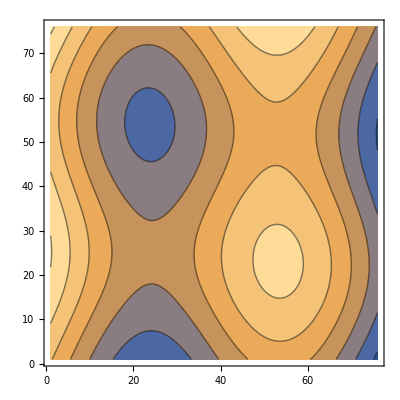

-Graphics3D-

```mathematica
k=9;
psik=ArrayReshape[evecmat[[-k]],{Nyv+1, Nxv+1}];
evalk=evalvec[[-k]];
ListPlot3D[{Flatten[xx],Flatten[yy],Flatten[psik]}ᵀ]
ListContourPlot[psik]
ListPlot3D[Differences[Differences[psik,{0,1}],{0,1}]]
```

```mathematica
(*
k=1;
psik=ArrayReshape[evecmat[[-k]],{Nyv-3, Nxv-3}];
ListPlot3D[psik]
*)
```

```mathematica
psixyk=Interpolation[{{Flatten[xx],Flatten[yy]}ᵀ,Flatten[psik]}ᵀ,InterpolationOrder->6]
```

InterpolatingFunction[{{0., 0.5}, {0., 0.5}}, <>]

```mathematica
Plot3D[psixyk[x,y],{x,0,0.5},{y,0.,0.5}]
```

-Graphics3D-

```mathematica
DX2Y2=D[D[psixyk[x,y],{y,2}],{x,2}];
DX4=D[D[psixyk[x,y],{x,2}],{x,2}];
DY4=D[D[psixyk[x,y],{y,2}],{y,2}];
Plot3D[(DX4+DY4+2DX2Y2)/evalk,{x,0,Lx},{y,0,Ly}]
```

-Graphics3D-

```mathematica
Export["/Users/Subhadeep_De/Box\ Sync/Mathematica_Data/FmatLx0.04Ly0.04Nx76Ny76.dat",Fmatsv]
```

```mathematica
Put[Fmats,"/Users/Subhadeep_De/Box\ Sync/Mathematica_Data/FmatsNx76Ny&6-h-nu"]
```

```mathematica
Fmatscheck=Get["/Users/Subhadeep_De/Box\ Sync/Mathematica_Data/FmatsNx76Ny76-h-nu"];
```